# Tutorial of Wolfram Quantum Framework

## Jarosław Miszczak 27/09/2023

## Package loading

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

## Pure and mixed states

```mathematica
?QuantumState
```

```mathematica
QuantumState["5"]["StateVector"]//Normal
```

{0,1}

```mathematica
ψ={{-Graphics-, QuantumState}}["PhiMinus"]
```

QuantumState[…]

```mathematica
ψ["PureStateQ"]
```

True

```mathematica
ψ["VonNeumannEntropy"]
```

0 b

```mathematica
ψ=QuantumState[{1,2ⅈ+1,3},3]
```

QuantumState[…]

```mathematica
ψ["Formula"]
```

0+(1+2 ⅈ) 1+3 2

## Random states

```mathematica
r=QuantumState["RandomMixed"]
```

QuantumState[…]

```mathematica
r["State"]//Normal
```

{{0.204816+0. ⅈ,0.316108-0.0990384 ⅈ},{0.316108+0.0990384 ⅈ,0.795184+0. ⅈ}}

```mathematica
r["Purity"]
```

0.893733

## Quantum gates

```mathematica
?QuantumOperator
```

```mathematica
cnot=QuantumOperator["CNOT",{3,4}]
```

QuantumOperator[…]

```mathematica
x=QuantumOperator["X",{3}]
```

QuantumOperator[…]

```mathematica
target={1,2};
ctrl1={3};
ctrl0={4,5};
cu=QuantumOperator[{"C","X"->{1,2},ctrl1,ctrl0}]
```

QuantumOperator[…]

```mathematica
cu["CircuitDiagram",ImageSize->50]
```

-Graphics-

```mathematica
mpl=QuantumOperator[{"Multiplexer",QuantumOperator[{"I",6}],QuantumOperator["NOT"]}]
```

QuantumOperator[…]

```mathematica
mpl["CircuitDiagram",ImageSize->100]
```

-Graphics-

## Measurements

```mathematica
ψ0=QuantumState[Sqrt@{-3,2,5},3]
```

QuantumState[…]

```mathematica
?QuantumMeasurementOperator
```

```mathematica
qmo=QuantumMeasurementOperator[QuantumBasis[ψ0["Dimensions"]]]
```

QuantumMeasurementOperator[…]

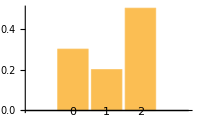

```mathematica
Show[m=qmo[ψ0]["ProbabilityPlot"],ImageSize->200]
```

## State estimation

```mathematica
?QuantumMeasurementSimulation
```

```mathematica
?QuantumStateSampler
```

```mathematica
?QuantumStateEstimate
```

```mathematica
state=QuantumState["RandomMixed"];
```

```mathematica
result=QuantumMeasurementSimulation[state,QuantumMeasurementOperator/@{"X","Y","Z"},100]
```

<|QuantumMeasurementOperator[…]→{3,97},QuantumMeasurementOperator[…]→{47,53},QuantumMeasurementOperator[…]→{73,27}|>

```mathematica
estimation=QuantumStateEstimate[result]
```

QuantumStateEstimation[…]

```mathematica
samples=estimation["BayesianSampler"][100];
```

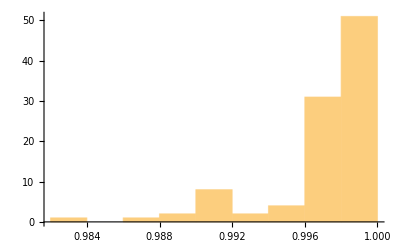

```mathematica
Histogram[QuantumDistance[#,state,"Fidelity"]&/@samples]
```